```mathematica
exp2[j_,m_]:= m *j(j+1)
```

```mathematica
A=MatrixForm[Table[Table[exp1[i,m],{i,-5,5}],{m,-3,3}]]
```

(-60 | -36 | -18 | -6 | 0 | 0 | -6 | -18 | -36 | -60 | -90
-40 | -24 | -12 | -4 | 0 | 0 | -4 | -12 | -24 | -40 | -60
-20 | -12 | -6 | -2 | 0 | 0 | -2 | -6 | -12 | -20 | -30
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
20 | 12 | 6 | 2 | 0 | 0 | 2 | 6 | 12 | 20 | 30
40 | 24 | 12 | 4 | 0 | 0 | 4 | 12 | 24 | 40 | 60
60 | 36 | 18 | 6 | 0 | 0 | 6 | 18 | 36 | 60 | 90)

```mathematica
γy=3γx;
```

```mathematica
HE[j_,m_,k_]:= (m+1/4(γx/(2j-1))(√(j(j+1)-m(m+1))+√(j(j+1)-m(m-1)))^2-1/4(γy/(2j-1))(√(j(j+1)-m(m+1))-√(j(j+1)-m(m-1)))^2)KroneckerDelta[m,k]
```

```mathematica
j=20;
H=Table[Table[HE[j,m,k],{m,j,-j,-1}],{k,j,-j,-1}];
```

```mathematica
A=Eigenvalues[H];
```

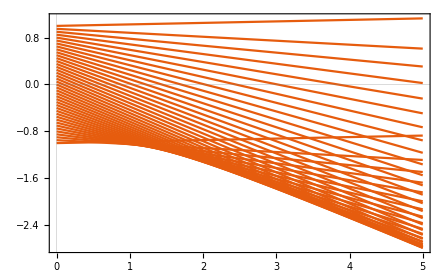

```mathematica
Plot[-A/j,{γx,0,5},PlotTheme->"Scientific",PlotRange->All]
```

```mathematica
h=1;
HE1[j_,m_,k_]:=(m h- h^2/2(γx/(2 j-1))((j(j+1)-(m-2)(m-1))-4 √(j(j+1)-m(m+1))√(j(j+1)-m(m-1))+(j(j+1)-(m+2)(m+1))))KroneckerDelta[k,m]
```

```mathematica
j=20;
H=Table[Table[HE1[j,m,k],{m,j,-j,-1}],{k,j,-j,-1}];
```

```mathematica
CE=Eigenvalues[H];
```

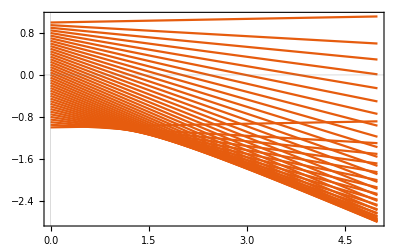

```mathematica
Plot[-CE/j,{γx,0,5},PlotTheme->"Scientific",PlotRange->All]
```

```mathematica
f[x_]:= x^2;
g[x_]:=x^3;
h[x_]:=x;
```

```mathematica
xrange = Range[-5,5,0.1];
ListOfFun ={f[x],g[x],h[x]}
```

{x^2,x^3,x}

```mathematica
ListOfFun[[1]]
```

x^2

```mathematica
ListOfFun[[1]]/. x->1
```

1

```mathematica
xrange=Range[-5,5,0.1];
```

```mathematica
Lista1= Table[Transpose[{xrange,Table[ListOfFun[[i]]/. x-> k,{k,-5,5,0.1}]}],{i,1,3}];
```

```mathematica
`
```

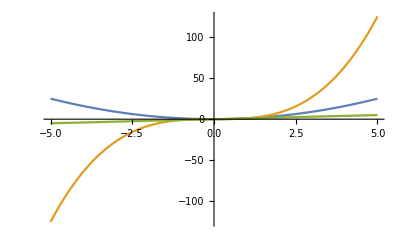

```mathematica
ListLinePlot[Lista1,PlotRange-> All]
```

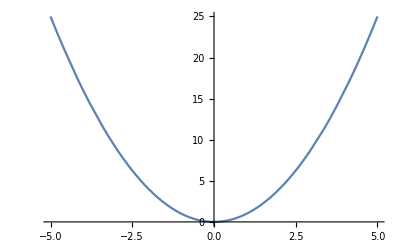

```mathematica
Plot[x^2,{x,-5,5},PlotPoints->4]
```